```mathematica
X={1,1,0,0,0,1,1,2,1,1,1,0,2,2,4,3,2,0,2,2,2,2,3,1,0,2,0,5,3,6,2,1,2,1,8,11,5,8,12,15,22,48,50,73,92,108,113,149,123,97,75,34,6};
n=Length[X]
```

53

-3.79809+0.162505 t

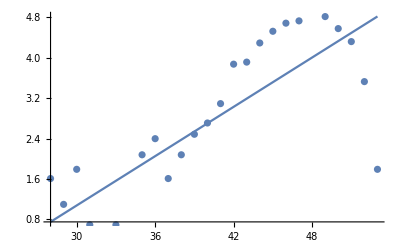

0.288207

{{a→0.226244}}

0.228661

-5.93361

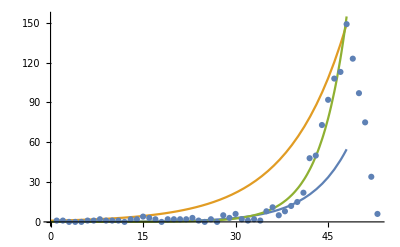

```mathematica
Fit[Table[{k,Log[X[[k]]]},{k,28,n}],{1,t},t]
Show[Plot[%,{t,28,n}],ListPlot[Table[{t,Log[X[[t]]]},{t,28,n}]]]
a=(Mean [Table[Log[X[[t]]]t,{t,33,49}]]-41Mean[Table[Log[X[[t]]],{t,33,49}]])/(Mean[Table[t^2,{t,33,49}]]-41^2)//N
Clear[a];NSolve[Sum [X[[t]]Exp[a*t]t,{t,48}]/Sum [Exp[2a*t]t,{t,48}]==Sum[X[[t]]Exp[a*t],{t,48}]/Sum [Exp[2a*t],{t,48}],a,Reals]
Clear[a];a=a/.Flatten[NSolve[Sum [X[[t]]Exp[a*t]t,{t,33,48}]/Sum [Exp[2a*t]t,{t,48}]==Sum[X[[t]]Exp[a*t],{t,33,48}]/Sum [Exp[2a*t],{t,48}],a,Reals]]
b=Log[Sum [X[[t]]Exp[a*t]t,{t,33,48}]/Sum [Exp[2a*t]t,{t,48}]]
Show[Plot[{Exp[%%%%%%],149^((t-1)/47),Exp[a*t+b]},{t,0,48},PlotRange->All],ListPlot[Table[{t,X[[t]]},{t,n}]],PlotRange->All]
```

```mathematica
RootApproximant[0.22866149551833367]
```

Root[5-262 #1^2+458 #1^3+1179 #1^4&,4]

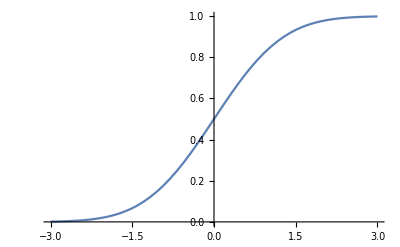

```mathematica
Plot[(1+Erf[ϵ/√2])/2,{ϵ,-3,3}]
```

(ⅇ^(-ϵ^2/2))/(√(2 π))

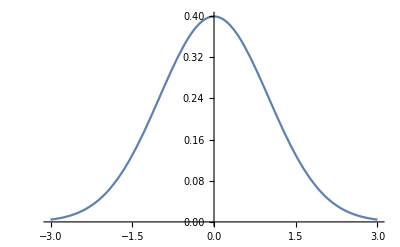

```mathematica
D[(1+Erf[ϵ/Sqrt[2]])/2,ϵ]
Plot[%,{ϵ,-3,3}]
```

```mathematica
Res1=Table[X[[t]]-Exp[a*t+b],{t,32,48}]
nr=Length[Res1];
m=Mean[Res1];
s=StandardDeviation[Res1];
Dn=Max[Max[Table[k/nr-(Erf[(Sort[Res1][[k]]-m)/s/Sqrt[2]]+1)/2,{k,nr}]],Max[Table[(Erf[(Sort[Res1][[k]]-m)/s/Sqrt[2]]+1)/2-(k-1)/nr,{k,nr}]]]
Sqrt[nr]Dn
```

{-2.98906,-3.01391,-5.30207,0.0788241,1.04374,-7.51418,-7.72928,-7.7704,-9.84974,-9.23404,8.74142,0.655237,10.9778,14.0432,10.0148,-10.1592,-5.8008}

0.167689

0.691401

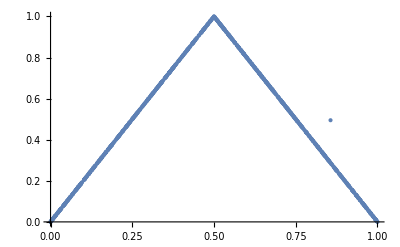

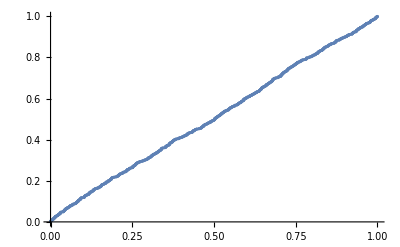

```mathematica
n=1000;
W=Table[Random[],{n}]; 
Z=W;
Do[W[[k+1]]=4W[[k]](1-W[[k]]);Z[[k+1]]=1/2+ArcSin[2W[[k+1]]-1]/Pi,{k,n-1}];
ListPlot[Table[{Z[[k]],Z[[k+1]]},{k,n-1}]]
ListPlot[Table[{Sort[Z][[k]],k/(n+1)},{k,n}]]
```

```mathematica
V=Pi//N; 
Do[V=FractionalPart[2V];Print[V],{60}]
```

0.283185

0.566371

0.132741

0.265482

0.530965

0.0619298

0.12386

0.247719

0.495439

0.990877

0.981755

0.963509

0.927018

0.854036

0.708073

0.416146

0.832291

0.664583

0.329165

0.658331

0.316661

0.633322

0.266645

0.533289

0.0665783

0.133157

0.266313

0.532626

0.0652523

0.130505

0.261009

0.522018

0.0440369

0.0880737

0.176147

0.352295

0.70459

0.40918

0.818359

0.636719

0.273438

0.546875

0.09375

0.1875

0.375

0.75

0.5

0.

0.

0.

«10 more identical outputs»

```mathematica
Sum[1/X-Log[1+1/X],{X,Infinity}]
%//N
```

EulerGamma

0.577216

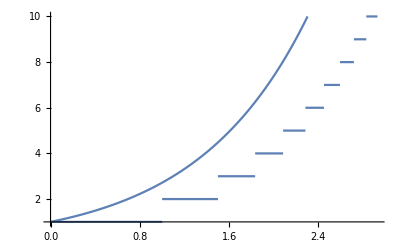

```mathematica
Show[Plot[Exp[x],{x,0,Log[10]}],Table[Plot[k,{x,Sum[1/j,{j,k-1}],Sum[1/j,{j,k}]}],{k,10}],PlotRange->All]
```

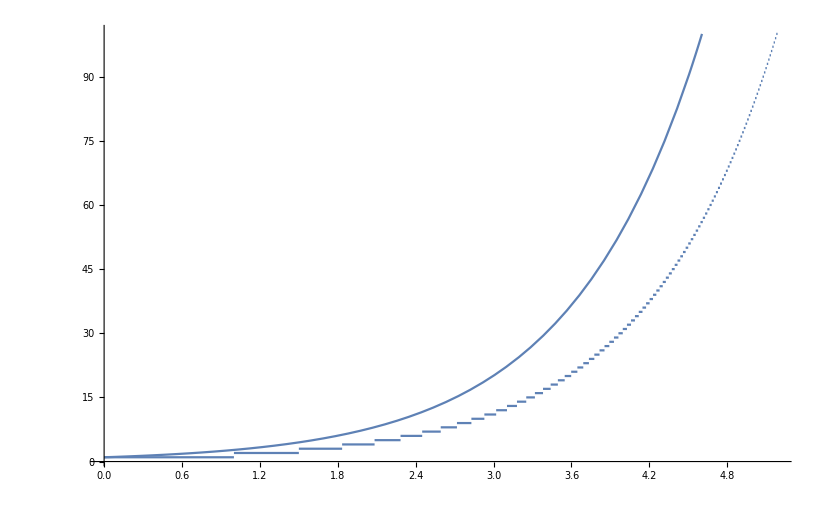

```mathematica
Show[Plot[Exp[x],{x,0,Log[100]}],Table[Plot[k,{x,Sum[1/j,{j,k-1}],Sum[1/j,{j,k}]}],{k,100}],PlotRange->All]
```

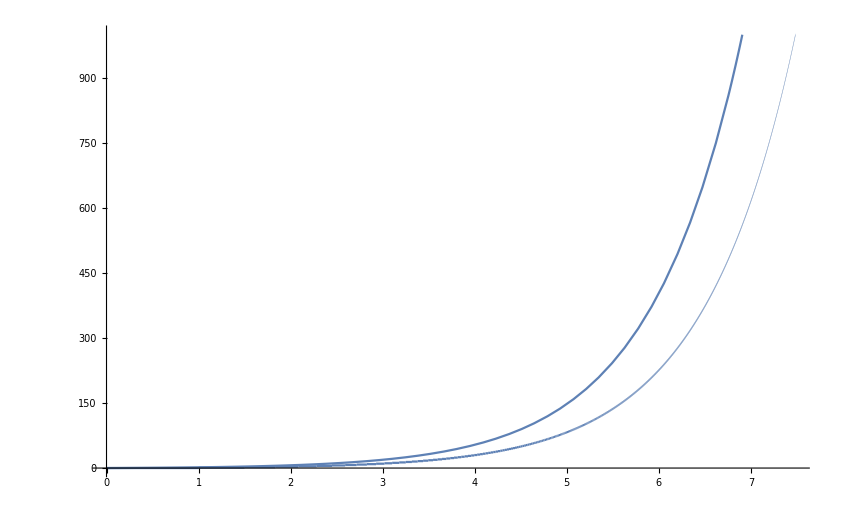

```mathematica
Show[Plot[Exp[x],{x,0,Log[1000]},PlotRange->All],Table[Plot[k,{x,Sum[1/j,{j,k-1}],Sum[1/j,{j,k}]}],{k,1000}],PlotRange->All]
```

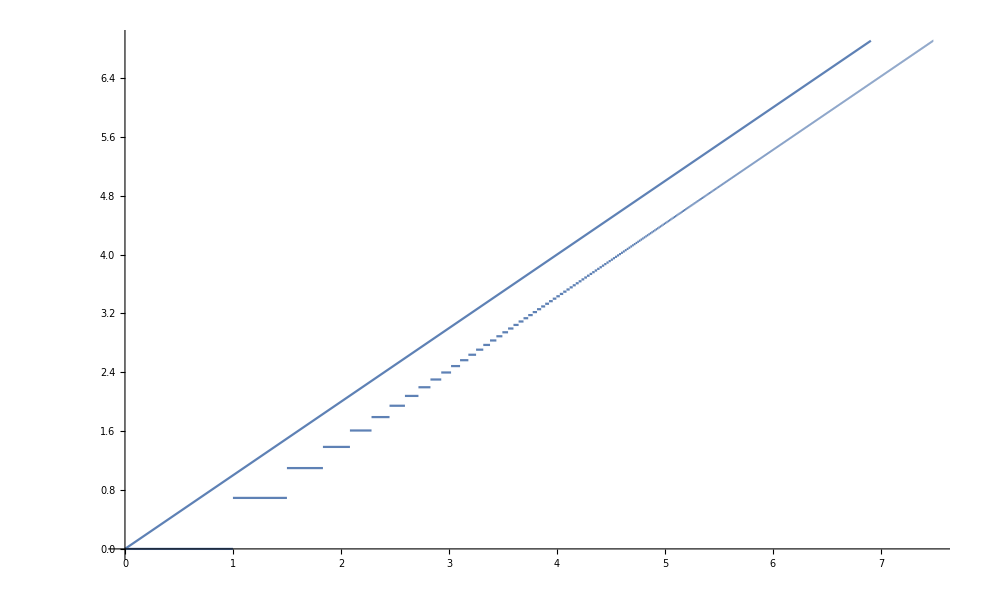

```mathematica
Show[Plot[x,{x,0,Log[1000]},PlotRange->All],Table[Plot[Log[k],{x,Sum[1/j,{j,k-1}],Sum[1/j,{j,k}]}],{k,1000}],PlotRange->All]
```

```mathematica
DSolve[{X'[t]==X(1-X/Ntotal)λ,X[0]==X0},X[t],t]
```

DSolve::dvnoarg: The function X appears with no arguments.

DSolve[{X'[t]==X (1-X/Ntotal) λ,X[0]==X0},X[t],t]

```mathematica
Integrate [1/(1-x*y),{x,0,1},{y,0,1}]
Sum[1/k^2,{k,1,Infinity}]
```

π^2/6

π^2/6

```mathematica
DSolve[{X'[R]==B(1-(X[R]+R)/Ntotal)-1,X[0]==X0},X[R],R]
Solve[(X[R]/.%)==0,R]
```

{{X[R]→ⅇ^(-(B R)/Ntotal) (-Ntotal+ⅇ^((B R)/Ntotal) Ntotal-ⅇ^((B R)/Ntotal) R+X0)}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→(Ntotal (B+ProductLog[-(B ⅇ^-B (Ntotal-X0))/Ntotal]))/B}}

10000 (1+1/2 ProductLog[-999/(500 ⅇ^2)])

NIntegrate::nlim: r = R is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

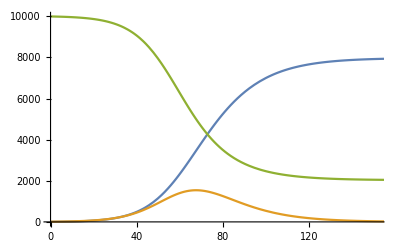

```mathematica
Ntotal=10000;
X0=10;
l=1/5;
b=1/10;
X[R_]:=Ntotal-R-(Ntotal-X0)Exp[-l/b*R/Ntotal];
t[R_]:=NIntegrate[1/X[r],{r,0,R}]/b;
RInf=Ntotal(1+ProductLog[0,-l/b(1-X0/Ntotal)Exp[-l/b]]b/l)
ParametricPlot[{{t[R],R},{t[R],X[R]},{t[R],Ntotal-X[R]-R}},{R,0,Floor[RInf]},AspectRatio->1/GoldenRatio]
```

Ntotal (1+ProductLog[-B ⅇ^-B (1-X0/Ntotal)]/B)

800.204

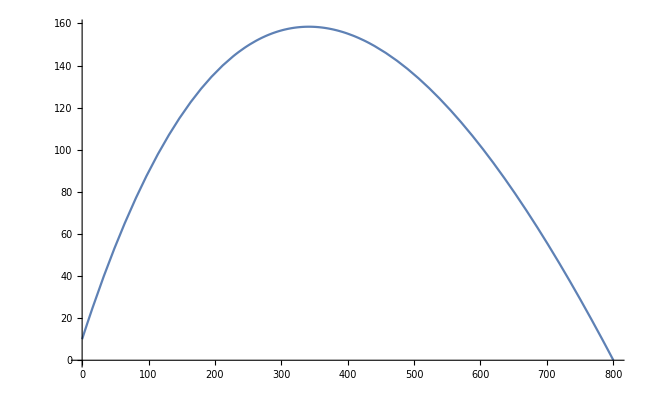

19.7071

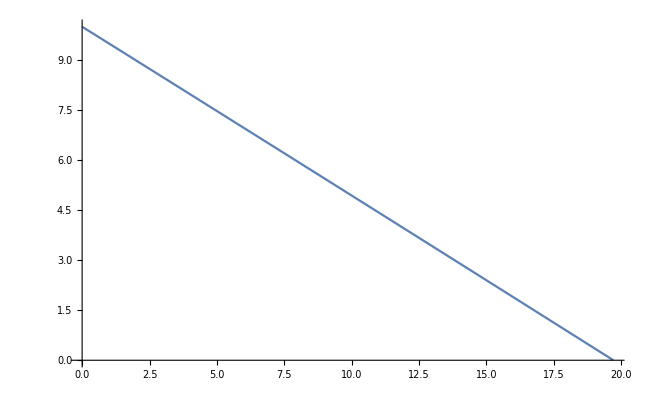

```mathematica
X[R_]:=Ntotal-R-(Ntotal-X0)Exp[-B*R/Ntotal];
Rinf=Ntotal(1+ProductLog[0,-B(1-X0/Ntotal)Exp[-B]]/B)
%/.{Ntotal->1000,X0->10,B->2}//N
Plot[X[R]/.{Ntotal->1000,X0->10,B->2},{R,0,Rinf/.{Ntotal->1000,X0->10,B->2}}]
Rinf/.{Ntotal->1000,X0->10,B->1/2}//N
Plot[X[R]/.{Ntotal->1000,X0->10,B->1/2},{R,0,Rinf/.{Ntotal->1000,X0->10,B->1/2}}]
```

```mathematica
Simplify[ⅇ^(-(B R)/Ntotal) (-Ntotal+ⅇ^((B R)/Ntotal) Ntotal-ⅇ^((B R)/Ntotal) R+X0)]
```

Ntotal-ⅇ^(-(B R)/Ntotal) Ntotal-R+ⅇ^(-(B R)/Ntotal) X0

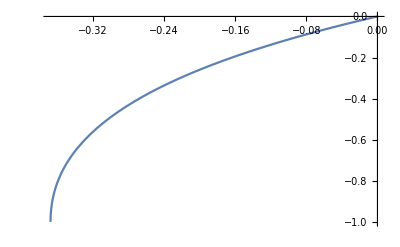

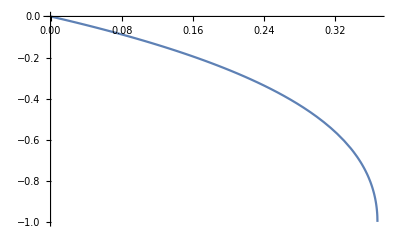

```mathematica
Plot[ProductLog[x],{x,-1/E,0}]
Plot[ProductLog[-x],{x,0,1/E}]
```